## SSS1. Mathematica Basics

## Table of Contents

Welcome to your first Mathematica Structured Study Session. Just as you did for Python last semester, we want to give you a space and material to help you gain essential skills and practice them.
The notebooks are divided into two sections just as last semester Lab(A) and Exercises(B). The lab will introduce new concepts and have examples, that will help you figure out the exercises yourself.

## A. Mathematica Lab

### Data Types

Maybe you remember from python that it is an object-oriented programming language that has various data types/object types, like Strings, Numbers, Lists, etc.

Mathematica does also have strings, numbers, lists, and many of the same types, but very importantly it is not an object-oriented programming language. If you go down to the source-code you will only find a few “atomic”(non-reducible) types: numbers(split into a few different types like Integers or Reals), strings, and symbols(which can be a lot of things). All of them are expressions and can be combined into new Expressions to make incredibly intricate data structures, display programs not just as text like in python and some other cool advantages that I hope you will learn to appreciate.

#### The structure of Mathematica

-Expressions
	- Numbers
		- Integers
		-Reals
	- Strings
	-symbols
		- empty Lists
		- empty Associations (aka Dictionaries)
		- Booleans
		- +, -, /, *,<,>
		-variables
		-...
	-image
	-graphs
	-combinations of numbers, strings, symbols,....
	-functions

Let’s look at a small example:
To display what a random mathematical expression looks like for Mathematica actually you can use the function FullForm

FullForm of a mathematical expression:

```mathematica
FullForm[x^2+(y √2)/4-6*y]
```

Plus[Power[x,2],Times[-6,y],Times[Rational[1,2],Power[2,Rational[-1,2]],y]]

It is hard to see what’s going on just using times, but luckily there is a function that does the same thing displayed in a nicer way

TreeForm of mathematical expression

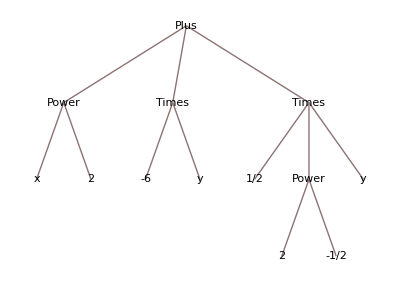

```mathematica
TreeForm[x^2+(y √2)/4-6*y]
```

You can see how the expression is internally broken up into the atomic pieces of numbers (like 2 or -6) and symbols (y or x). They are then combined by other symbols like Plus, Power or Times.
Try typing an expression yourself and look at the FullForm or TreeForm.

If you are more curious about how everything can be an expression, try the “Everything is an Expression”-Tutorial in the official documentation